## Computer Preliminaries and Error Descriptions

Unfortunately computers can't store numbers with infinite precision, but instead use an approximation that can be packed into a fixed number of bits.  These bits can be arranged to represent different data types usually called fixed point numbers or integers and floating point numbers.  Of most importance to us as numerical analysts are floating point numbers.  

A floating point number is represented within the computer as a bit sign (positive or negative), an integer number representing the number of significant digits called the significand or mantissa, and an integer exponent.  Symbolically, we might write:

s × M × B^sE

where, sis the sign, M is the mantissa, B is called the base usually 2, but sometimes 10 or 16, and E is the integer exponent.

The smallest floating point number which, when added to the floating point number 1.0, produces a result different than 1.0 is called the machine precision or machine epsilon, ϵ_m.  Most modern computers have a machine epsilon value somewhere around 2^-53(1.11× 10^-16), although ϵ_m can range depending on the base and the bit wordlength (32-bit, 64-bit, etc.)

Almost any arithmetic between floating point numbers will produce an additional fraction error of size ϵ_m, this error is called roundoff error.

◀     |     ▶

## The Numerical Analyst's Enemy: Truncation Error

Roundoff error is a characteristic of computer hardware; however there is another type of error that is completely a result of the algorithm or software.

Most numerical algorithms compute discrete approximations to a continuous desired quantity.  An example of this is the use of the Taylor series to approximate the function sin(x). The Taylor series approximation of the function is as follows:

sin(x) = x - x^3/(3!)+x^5/(5!)-x^7/(7!) ... 

Of course, this representation requires that the series be infinite for the solution to be exact.  Even the best computers cannot evaluate an infinite number of terms in the Taylor series therefore we must take a finite number of terms for the approximation.  The difference between the approximated answer and the exact solution is called the truncation error.  Let's take a look at some numerics, we all know that sin(π/2) = 1.

We start by defining a function representing the Taylor series expansion of sin(x).

```mathematica
TaylorSin[x_,nt_]:=∑_(n=0)^nt (-1)^n/((2n+1)!)x^(2n+1)
```

By evaluating the function above at x = π/2 and subtracting it from 1 we can see how the truncation error evolves as we add more terms in the Taylor series.

```mathematica
trunError=Manipulate[
Column[{TaylorSin[x,nt]," ",
Sin[π/2]-Re[TaylorSin[π/2,nt]]}],{{nt,1,"No. of terms"},1,9,1,Appearance->"Labeled"},TrackedSymbols:>{nt},SaveDefinitions->True]//N
```

Here is an interesting visualization of how the difference between the two functions evolves as we add more terms of the Taylor series.  The truncation error is visualized as the maximum difference between the two curves.

```mathematica
Manipulate[Column[{TaylorSin[x,nt]," ",Plot[{Sin[x],TaylorSin[x,nt]},{x,0,2π},PlotRange->{{0,2π},{-1,1}},ImageSize->Medium]}],{{nt,1,"No. of terms"},1,9,1,Appearance->"Labeled"},TrackedSymbols:>{nt},SaveDefinitions->True]
```

The minimization of truncation error is one of the main goals of numerical analysis.

◀     |     ▶

## Stability

Usually roundoff error and truncation error do not interact with each other, but sometimes roundoff error can cause a numerical algorithm to become unstable.  This happens when roundoff error gets mixed into the calculation and is magnified as it continues.  Let's look at an example:

Suppose we want to calculate the powers of the so called "Golden Mean"

ϕ = (√5-1)/2

It can be verified that the powers ϕ^n can be calculated using the simple recursion relationship,

ϕ^(n+1)= ϕ^(n-1)- ϕ^n

Therefore by calculating ϕ^0= 1 and ϕ^1= 0.618034 and successively applying the recursion relationship we should be able to calculate as many powers as desired.  Let's see this in action:

First we'll calculate what we'll call the "exact" answer by actually evaluating all the powers individually.

```mathematica
ϕexact=Table[((√5-1)/2)^n,{n,0,80}];
```

Next we'll calculate the first 2 powers then use the recursion formula to evaluate the rest.

```mathematica
ϕrecursion=Join[{1,(√5-1)/2},ConstantArray[0,79]];
Do[
ϕrecursion[[n+1]]=ϕrecursion[[n-1]]-ϕrecursion[[n]]
,{n,2,70}
]
```

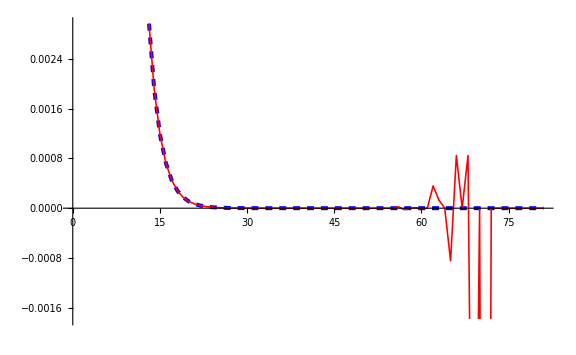

```mathematica
<<PlotLegends`
ListLinePlot[{ϕexact,ϕrecursion},PlotStyle->{{Dashed,Blue,Thickness[0.005]},{Red,Thickness[0.002]}},ImageSize->Large]
```

The recursion relationship is unstable and cannot be used as stated to solve this problem.  Stability of algorithms is something we always need to be aware of as numerical analysts.

◀     |     ▶

## Psuedocode

Psuedocode is a compact and informal way of describing a numerical algorithm.  It utilizes the conventional structure of a programming language (loops, conditional statements, etc.) but is intended for human reading.

◀     |     ▶

## Conventional Programming Structures

Do Loops and For Loops:  These two structures essentially do the same thing in a slightly different way.  They are used when you want to do something in sequence for a set number of iterations.  Let's look at a couple of examples using Mathematica.

```mathematica
Do[
Print[i];
Pause[1];
,{i,1,10,2}
]
```

1

3

5

7

9

```mathematica
i=.;For[i=0,i<10,i=i+2,
Print[i]
Pause[1]
]
```

0

2

4

6

8

◀     |     ▶

## Conventional Programming Structures (cont.)

While Loops:  These loops are used to evaluate the body of the loop as long as a certain test is passed.  An example:

```mathematica
i=0;
While[i<10,
Print[i];
Pause[1];
i=i+2;
]
```

0

2

4

6

8

If Statements: Used as tests to return different actions.  An example:

```mathematica
i=2;
If[i==1,Print["i is equal to 1"],Print["i is not equal to 1"]]
```

i is not equal to 1

When we write sophisticated code we might use multiple loops and if statements in conjunction.

```mathematica
i=0;
While[i<3,
If[i==1,Print["i is equal to 1"],Print["i is not equal to 1"]];
Pause[1];
i++;
]
```

i is not equal to 1

i is equal to 1

i is not equal to 1

◀     |     ▶